```mathematica
k=18.15;
SubPlus[W]=k/9;
SubMinus[W]=k-SubPlus[W];
SubPlus[p]=√(SubPlus[W]*SubPlus[W]-1);
SubMinus[p]=√(SubMinus[W]*SubMinus[W]-1);
α=1/137;
pmz=SubMinus[p]*Cos[θ];
pmx=SubMinus[p]*√(1-(Cos[θ])^2);

q=√((SubPlus[p]+pmz)*(SubPlus[p]+pmz)+pmx*pmx);
pmzye=SubMinus[p]*ye;
pmxye=SubMinus[p]*√(1-(ye)^2);
qye=√((SubPlus[p]+pmzye)*(SubPlus[p]+pmzye)+pmxye*pmxye);
e[l_,θ_]=(2*α)/(π*(l+1))*(SubPlus[p]*SubMinus[p])/q*(q/k)^(2*l-1)/((k^2-q^2)^2)*((2*l+1)*(SubPlus[W]*SubMinus[W]+1-1/3*SubPlus[p]*SubMinus[p]*Cos[θ])+l*(q^2/k^2-2)*(SubPlus[W]*SubMinus[W]-1+SubPlus[p]*SubMinus[p]*Cos[θ])+1/3(l-1)*SubPlus[p]*SubMinus[p]*(3/q^2*(SubMinus[p]+SubPlus[p]*Cos[θ])*(SubPlus[p]+SubMinus[p]*Cos[θ])-Cos[θ]));
m[l_,θ_]=(2*α)/π*(SubPlus[p]*SubMinus[p])/q*(q/k)^(2*l+1)/((k^2-q^2)^2)*(1+SubPlus[W]*SubMinus[W]-(SubPlus[p]*SubMinus[p])/q^2*(SubMinus[p]+SubPlus[p]*Cos[θ])*(SubPlus[p]+SubMinus[p]*Cos[θ]));
ecos[l_,ye_]=(2*α)/(π*(l+1))*(SubPlus[p]*SubMinus[p])/qye*(qye/k)^(2*l-1)/((k^2-qye^2)^2)*((2*l+1)*(SubPlus[W]*SubMinus[W]+1-1/3*SubPlus[p]*SubMinus[p]*ye)+l*(qye^2/k^2-2)*(SubPlus[W]*SubMinus[W]-1+SubPlus[p]*SubMinus[p]*ye)+1/3(l-1)*SubPlus[p]*SubMinus[p]*(3/qye^2*(SubMinus[p]+SubPlus[p]*ye)*(SubPlus[p]+SubMinus[p]*ye)-ye));
mcos[l_,ye_]=(2*α)/π*(SubPlus[p]*SubMinus[p])/qye*(qye/k)^(2*l+1)/((k^2-qye^2)^2)*(1+SubPlus[W]*SubMinus[W]-(SubPlus[p]*SubMinus[p])/qye^2*(SubMinus[p]+SubPlus[p]*ye)*(SubPlus[p]+SubMinus[p]*ye));
```

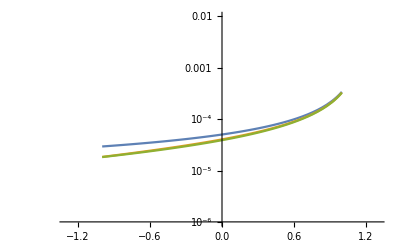

```mathematica
LogPlot[{ecos[1,ye],ecos[2,ye],mcos[1,ye]},{ye,-1,1},PlotRange->{{-1.3,1.3},{10^-6,10^-2}}]
```

```mathematica
distM=ProbabilityDistribution[m[1,θ],{θ,0,Pi}];
```

```mathematica
PDF[distM,θ]
```

```mathematica
Piecewise[{{(0.000021916482521588842 ((1.751269380890457+16.10231177329654 Cos[θ])^2+259.28444444444443 (1-Cos[θ]^2)) (33.535555555555554-(28.19948557012615 (16.10231177329654+1.751269380890457 Cos[θ]) (1.751269380890457+16.10231177329654 Cos[θ]))/((1.751269380890457+16.10231177329654 Cos[θ])^2+259.28444444444443 (1-Cos[θ]^2))))/((329.42249999999996-(1.751269380890457+16.10231177329654 Cos[θ])^2-259.28444444444443 (1-Cos[θ]^2))^2), 0<θ<π}, {0, True}}]
```

Piecewise[{{(0.0000219165 ((1.75127+16.1023 Cos[θ])^2+259.284 (1-Cos[θ]^2)) (33.5356-(28.1995 (16.1023+1.75127 Cos[θ]) (1.75127+16.1023 Cos[θ]))/((1.75127+16.1023 Cos[θ])^2+259.284 (1-Cos[θ]^2))))/((329.422-(1.75127+16.1023 Cos[θ])^2-259.284 (1-Cos[θ]^2))^2), 0<θ<π}, {0, True}}]

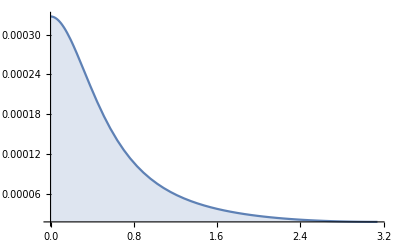

```mathematica
Plot[PDF[distM,θ],{θ,0,Pi},Filling->Axis,PlotRange->All]
```

```mathematica
nTuples={};
energies={};

k=18.15;
α=1/137;
```

```mathematica
randoms=RandomReal[{1,k-1},1000000];
```

```mathematica
energies=Table[{randoms[[i]],k-randoms[[i]],√(randoms[[i]]*randoms[[i]]-1),√((k-randoms[[i]])*(k-randoms[[i]])-1),√((k-randoms[[i]])*(k-randoms[[i]])-1)*Cos[θ],√((k-randoms[[i]])*(k-randoms[[i]])-1)*√(1-(Cos[θ])^2),√((√(randoms[[i]]*randoms[[i]]-1)+√((k-randoms[[i]])*(k-randoms[[i]])-1)*Cos[θ])*(√(randoms[[i]]*randoms[[i]]-1)+√((k-randoms[[i]])*(k-randoms[[i]])-1)*Cos[θ])+√((k-randoms[[i]])*(k-randoms[[i]])-1)*√(1-(Cos[θ])^2)*√((k-randoms[[i]])*(k-randoms[[i]])-1)*√(1-(Cos[θ])^2))},{i,1,1000000}];
```

```mathematica
For[i=1,i≤10,++i,
SubPlus[W]=energies[[i,1]];
SubMinus[W]=energies[[i,2]];
SubPlus[p]=energies[[i,3]];
SubMinus[p]=energies[[i,4]];
pmz=energies[[i,5]];
pmx=energies[[i,6]];
q=energies[[i,7]];

m[l_,θ_]=(2*α)/π*(SubPlus[p]*SubMinus[p])/q*(q/k)^(2*l+1)/((k^2-q^2)^2)*(1+SubPlus[W]*SubMinus[W]-(SubPlus[p]*SubMinus[p])/q^2*(SubMinus[p]+SubPlus[p]*Cos[θ])*(SubPlus[p]+SubMinus[p]*Cos[θ]));

distM=ProbabilityDistribution[m[1,θ],{θ,0,Pi}];
angle=RandomVariate[distM];
AppendTo[nTuples,{SubPlus[W],SubMinus[W],angle}]; 
]
```

```mathematica
l=1;
angles=Table[RandomVariate[ProbabilityDistribution[(2*α)/π*(energies[[x,3]]*energies[[x,4]])/energies[[x,7]]*(energies[[x,7]]/k)^(2*l+1)/((k^2-energies[[x,7]]^2)^2)*(1+energies[[x,1]]*energies[[x,2]]-(energies[[x,3]]*energies[[x,4]])/energies[[x,7]]^2*(energies[[x,4]]+energies[[x,3]]*Cos[θ])*(energies[[x,3]]+energies[[x,4]]*Cos[θ])),{θ,0,Pi}]],{x,1,1000000}];
```

$Aborted

```mathematica
finalData={};
For[i=1,i≤1000000,++i,
If[energies[[i,1]]>1 && energies[[i,2]] > 1,
AppendTo[finalData,{energies[[i,1]],energies[[i,2]],angles[[i]]}]];
]
```

```mathematica
finalData=Table[{energies[[i,1]],energies[[i,2]],angles[[i]]},{i,1,1000000}];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["priorRose.txt",Flatten[finalData]]
```

priorRose.txt

```mathematica
Length[finalData]
```

100

```mathematica
Length[energies]
```

0

```mathematica
energies
```

{{15.8743,2.27566,15.8428,2.04417,2.04417 Cos[θ],2.04417 √(1-Cos[θ]^2),√((15.8428+2.04417 Cos[θ])^2+4.17861 (1-Cos[θ]^2))},{12.8965,5.25347,12.8577,5.15742,5.15742 Cos[θ],5.15742 √(1-Cos[θ]^2),√((12.8577+5.15742 Cos[θ])^2+26.599 (1-Cos[θ]^2))},399997,{11.87,6.28,11.8278,6.19987,6.19987 Cos[θ],6.19987 √(1-Cos[θ]^2),√((11.8278+6.19987 Cos[θ])^2+38.4383 (1-Cos[θ]^2))}}
 |  |  |  |

{15.8743,12.8965,15.5647,8.85074,13.3109,9.04305,16.1008,8.93621,3.09548,5.30108,10.1382,5.18164,3.9983,2.07848,13.0805,1.58505,9.6269,11.3378,9.99069,7.1191,399960,12.6288,9.10049,4.67339,11.6335,15.5243,15.8584,10.4722,16.2913,3.92766,9.59583,7.11542,5.89265,12.1081,6.55052,1.14453,13.6497,12.8718,10.5778,15.6446,11.87}
 |  |  |  |

{{15.8743,2.27566,0.532403},{12.8965,5.25347,0.749221},{15.5647,2.58533,0.260819},{8.85074,9.29926,0.247878},{13.3109,4.83913,0.0290195},{9.04305,9.10695,0.113176},399988,{1.14453,17.0055,2.18438},{13.6497,4.50033,0.420118},{12.8718,5.27821,0.054449},{10.5778,7.57218,0.010889},{15.6446,2.50541,1.70602},{11.87,6.28,0.0320296}}
 |  |  |  |

LinkObject::linkd: Unable to communicate with closed link LinkObject[/usr/local/Wolfram/Mathematica/11.3/Executables/wolfram -subkernel -noinit -nopaclet -wstp,426,14].

Kernels::rdead: Subkernel connected through KernelObject[5,local] appears dead.

Kernels::rdead: Subkernel connected through KernelObject[5,local,<defunct>] appears dead.

LaunchKernels::clone: Kernel KernelObject[5,local,<defunct>] resurrected as KernelObject[7,local].

$Aborted